```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/benchmarks/benchmarks.csv"];
data=Take[data,{11,data//Length}];
headers=Partition[data[[1]],11];
cols=data[[1]];
data=Take[data,{2,data//Length}];
```

```mathematica
benchmarks={"bitonic_2n_float_sort_bench", "bitonic_8n_float_sort_bench","bitonic_float_sort_bench", "std_float_sort_bench", "hybrid_8n_float_sort_bench", "improved_bitonic_float_sort_bench"};
cols
```

{bitonic_2n_float_sort_bench/8,904019,746.364,746.946,ns,,,,,,8}

```mathematica
GetBenchData[name_]:=Block [{tab},
tab=Table[If[(StringPosition[data[[i,1]], name]//Length  && Length[data[[i]]]>5)≠0,data[[i]], ""],{i,1,data//Length}];
tab=DeleteCases[tab, ""];
Return [tab];
];
```

```mathematica
data;
```

```mathematica
data1=GetBenchData[benchmarks[[1]]];
data1=Take[data1, {1, (data1//Length)-2}];
timing1=data1[[All,4]];
NumToSort1=data1[[All,11]];
```

```mathematica
data2=GetBenchData[benchmarks[[2]]];
data2=Take[data2, {1, (data2//Length)-2}];
timing2=data2[[All,4]];
NumToSort2=data2[[All,11]];
```

```mathematica
data3=GetBenchData[benchmarks[[3]]];
data3=Take[data3, {1, (data3//Length)-2}];
timing3=data3[[All,4]];
NumToSort3=data3[[All,11]];
```

```mathematica
data4=GetBenchData[benchmarks[[4]]]
data4=Take[data4, {1, (data4//Length)-2}];
timing4=data4[[All,4]];
NumToSort4=data4[[All,11]]
```

{{std_float_sort_bench/10,679955,963.369,965.387,ns,,,,,,10},{std_float_sort_bench/20,498100,1456.32,1465.4,ns,,,,,,20},{std_float_sort_bench/40,270176,2478.1,2494.22,ns,,,,,,40},{std_float_sort_bench/50,219488,2905.81,2923.7,ns,,,,,,50},{std_float_sort_bench/80,119497,4672.58,4706.49,ns,,,,,,80},{std_float_sort_bench/100,115750,5578.41,5615.78,ns,,,,,,100},{std_float_sort_bench/200,57134,12208.8,12305.6,ns,,,,,,200},{std_float_sort_bench/400,26873,26048.7,26242.2,ns,,,,,,400},{std_float_sort_bench/800,9969,61806.1,62294.8,ns,,,,,,800},{std_float_sort_bench/1600,4943,125245,126017,ns,,,,,,1600},{std_float_sort_bench/3200,2520,275909,276941,ns,,,,,,3200},{std_float_sort_bench/5000,1575,435774,436824,ns,,,,,,5000},{std_float_sort_bench/7500,1009,721439,722323,ns,,,,,,7500},{std_float_sort_bench/10000,751,921618,922384,ns,,,,,,10000},{std_float_sort_bench/12000,607,1.12413×10^6,1.12479×10^6,ns,,,,,,12000},{std_float_sort_bench/15000,481,1.43545×10^6,1.43601×10^6,ns,,,,,,15000},{std_float_sort_bench/17000,342,1.95549×10^6,1.95641×10^6,ns,,,,,,17000},{std_float_sort_bench/20000,329,2.22608×10^6,2.22724×10^6,ns,,,,,,20000},{std_float_sort_bench/25000,261,2.59287×10^6,2.5932×10^6,ns,,,,,,25000},{std_float_sort_bench/27000,244,2.7882×10^6,2.78887×10^6,ns,,,,,,27000},{std_float_sort_bench/30000,215,3.12156×10^6,3.12246×10^6,ns,,,,,,30000},{std_float_sort_bench/35000,188,3.71933×10^6,3.71991×10^6,ns,,,,,,35000},{std_float_sort_bench/40000,151,4.30638×10^6,4.30721×10^6,ns,,,,,,40000},{std_float_sort_bench/50000,129,5.83464×10^6,5.82308×10^6,ns,,,,,,50000},{std_float_sort_bench/70000,84,8.91386×10^6,8.90163×10^6,ns,,,,,,70000},{std_float_sort_bench/100000,57,1.1713×10^7,1.17089×10^7,ns,,,,,,100000},{std_float_sort_bench/120000,45,1.45908×10^7,1.45923×10^7,ns,,,,,,120000},{std_float_sort_bench/150000,38,1.94258×10^7,1.94238×10^7,ns,,,,,,150000},{std_float_sort_bench/200000,26,2.46918×10^7,2.46931×10^7,ns,,,,,,200000},{std_float_sort_bench/400000,14,5.25206×10^7,5.2479×10^7,ns,,,,,,400000},{std_float_sort_bench/600000,9,8.27677×10^7,8.27685×10^7,ns,,,,,,600000},{std_float_sort_bench/800000,6,1.07672×10^8,1.0767×10^8,ns,,,,,,800000},{std_float_sort_bench/1000000,5,1.38109×10^8,1.38109×10^8,ns,,,,,,1.×10^6},{std_float_sort_bench/1200000,4,1.70197×10^8,1.70199×10^8,ns,,,,,,1.2×10^6},{std_float_sort_bench/1500000,3,2.15832×10^8,2.15835×10^8,ns,,,,,,1.5×10^6},{std_float_sort_bench/1800000,3,2.57627×10^8,2.57624×10^8,ns,,,,,,1.8×10^6},{std_float_sort_bench/2000000,2,2.85844×10^8,2.85842×10^8,ns,,,,,,2.×10^6},{std_float_sort_bench/2500000,2,3.66669×10^8,3.66666×10^8,ns,,,,,,2.5×10^6},{std_float_sort_bench/3000000,2,4.51558×10^8,4.51553×10^8,ns,,,,,,3.×10^6},{std_float_sort_bench/5000000,1,7.79964×10^8,7.79943×10^8,ns,,,,,,5.×10^6},{std_float_sort_bench/7000000,1,1.09634×10^9,1.09624×10^9,ns,,,,,,7.×10^6},{std_float_sort_bench/10000000,1,1.65501×10^9,1.65404×10^9,ns,,,,,,1.×10^7},{std_float_sort_bench/20000000,1,3.42038×10^9,3.41954×10^9,ns,,,,,,2.×10^7},{std_float_sort_bench/50000000,1,8.71735×10^9,8.71622×10^9,ns,,,,,,5.×10^7}}

{10,20,40,50,80,100,200,400,800,1600,3200,5000,7500,10000,12000,15000,17000,20000,25000,27000,30000,35000,40000,50000,70000,100000,120000,150000,200000,400000,600000,800000,1.×10^6,1.2×10^6,1.5×10^6,1.8×10^6,2.×10^6,2.5×10^6,3.×10^6,5.×10^6,7.×10^6,1.×10^7}

```mathematica
data5=GetBenchData[benchmarks[[5]]];
data5=Take[data5, {1, (data5//Length)-2}];
timing5=data5[[All,4]];
NumToSort5=data5[[All,11]];
```

```mathematica
data6=GetBenchData[benchmarks[[6]]];
data6=Take[data6, {1, (data6//Length)-2}];
timing6=data6[[All,4]];
NumToSort6=data6[[All,11]];
```

```mathematica
p1=Transpose[{NumToSort1,timing1}];
p2=Transpose[{NumToSort2,timing2}];
p3=SortBy[Transpose[{NumToSort3,timing3}], First]
p4=SortBy[Transpose[{NumToSort4,timing4}], First];
p5=SortBy[Transpose[{NumToSort5,timing5}], First];
p6=SortBy[Transpose[{NumToSort6,timing6}], First]
```

{{10,781.2},{10,794.283},{20,984.515},{20,992.386},{40,1171.95},{40,1199.15},{50,1434.55},{50,1488.48},{80,1593.38},{80,1702.31},{100,2222.79},{100,2332.29},{200,3156.56},{200,3444},{400,6465.26},{400,7204.07},{800,13763.4},{800,15761},{1600,30428.7},{1600,33749.7},{3200,68787.8},{3200,79024.1},{5000,123200},{5000,140503},{7500,262084},{7500,277634},{10000,272350},{10000,323589},{12000,324369},{12000,361482},{15000,407855},{15000,494553},{17000,516166},{17000,649129},{20000,643310},{20000,687799},{25000,766421},{25000,863482},{27000,829959},{27000,964260},{30000,924622},{30000,1.17012×10^6},{35000,1.19387×10^6},{35000,1.43696×10^6},{40000,1.36824×10^6},{40000,1.62581×10^6},{50000,1.70367×10^6},{50000,1.97215×10^6},{70000,2.68294×10^6},{70000,3.19238×10^6},{100000,3.79047×10^6},{100000,4.68703×10^6},{120000,5.0434×10^6},{120000,5.73551×10^6},{150000,6.34619×10^6},{150000,8.17501×10^6},{200000,8.53138×10^6},{200000,1.15419×10^7},{400000,1.94915×10^7},{400000,2.46703×10^7},{600000,3.12636×10^7},{600000,3.86416×10^7},{800000,4.39042×10^7},{800000,5.43833×10^7},{1.×10^6,5.49757×10^7},{1.×10^6,6.10818×10^7},{1.2×10^6,7.24601×10^7},{1.2×10^6,9.42368×10^7},{1.5×10^6,9.40549×10^7},{1.5×10^6,1.20139×10^8},{1.8×10^6,1.1217×10^8},{1.8×10^6,1.28555×10^8},{2.×10^6,1.22661×10^8},{2.×10^6,1.45332×10^8},{2.5×10^6,1.73629×10^8},{2.5×10^6,1.98362×10^8},{3.×10^6,2.03522×10^8},{3.×10^6,2.46779×10^8},{5.×10^6,3.81488×10^8},{5.×10^6,4.06288×10^8},{7.×10^6,5.55493×10^8},{7.×10^6,6.13012×10^8},{1.×10^7,8.96484×10^8},{1.×10^7,1.01311×10^9},{2.×10^7,2.02063×10^9},{5.×10^7,5.24929×10^9}}

{{10,794.283},{20,992.386},{40,1199.15},{50,1488.48},{80,1702.31},{100,2332.29},{200,3444},{400,7204.07},{800,15761},{1600,33749.7},{3200,79024.1},{5000,140503},{7500,277634},{10000,323589},{12000,361482},{15000,494553},{17000,649129},{20000,687799},{25000,863482},{27000,964260},{30000,1.17012×10^6},{35000,1.43696×10^6},{40000,1.62581×10^6},{50000,1.97215×10^6},{70000,3.19238×10^6},{100000,4.68703×10^6},{120000,5.73551×10^6},{150000,8.17501×10^6},{200000,1.15419×10^7},{400000,2.46703×10^7},{600000,3.86416×10^7},{800000,5.43833×10^7},{1.×10^6,6.10818×10^7},{1.2×10^6,9.42368×10^7},{1.5×10^6,1.20139×10^8},{1.8×10^6,1.28555×10^8},{2.×10^6,1.45332×10^8},{2.5×10^6,1.98362×10^8},{3.×10^6,2.46779×10^8},{5.×10^6,4.06288×10^8},{7.×10^6,6.13012×10^8},{1.×10^7,1.01311×10^9}}

```mathematica
color=ColorData[10,"ColorList"];
LegendFontSize=20;
legenda=
PointLegend[{
{color[[1]],AbsolutePointSize[8]},
{color[[2]],AbsolutePointSize[8]},
{color[[3]],AbsolutePointSize[8]},
{color[[4]], AbsolutePointSize[8]},
{color[[5]], AbsolutePointSize[8]},
{color[[6]], AbsolutePointSize[8]},
Directive[color[[9]], AbsolutePointSize[8]]},
{Style["bitonic 2^n sort", LegendFontSize], Style["bitonic 8n sort", LegendFontSize], Style["bitonic arbitrary n sort", LegendFontSize], 
Style["std sort", LegendFontSize], Style["hybrid 8n sort", LegendFontSize],  Style["bitonic sort ver2", LegendFontSize]},
LegendLabel->"", LegendLayout->{"Row",6}];
```

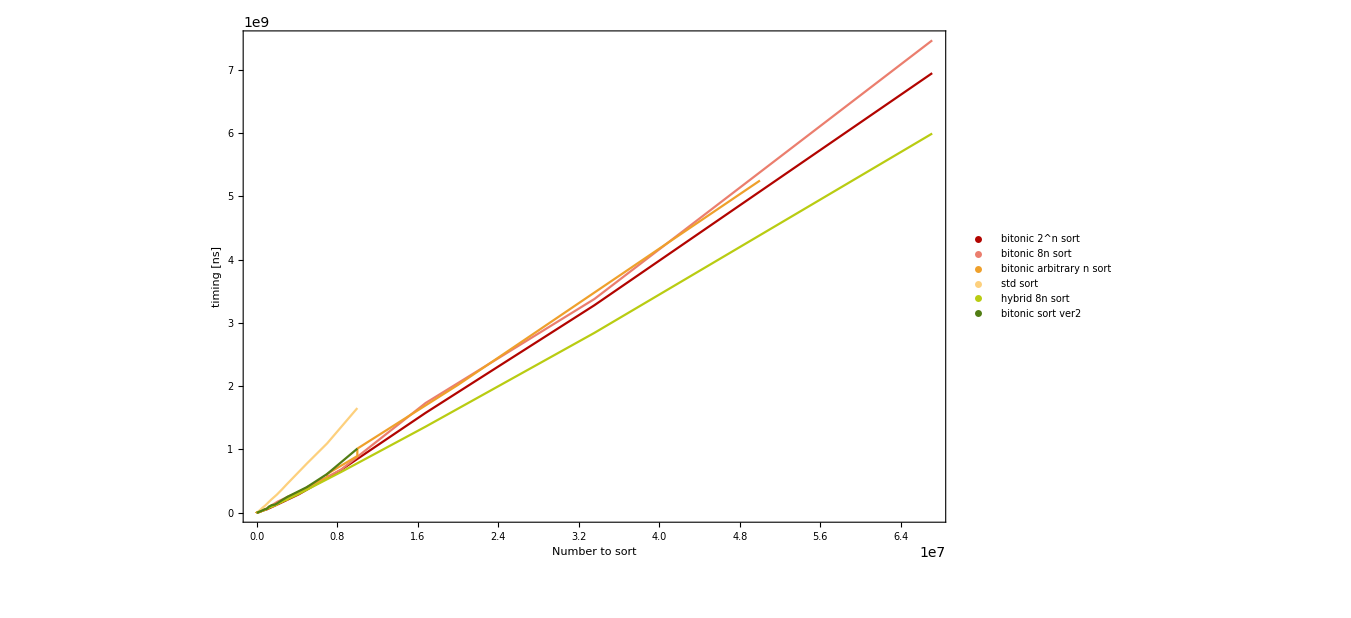

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4, p5, p6
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {1*10^7, 4*10^9}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->All,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

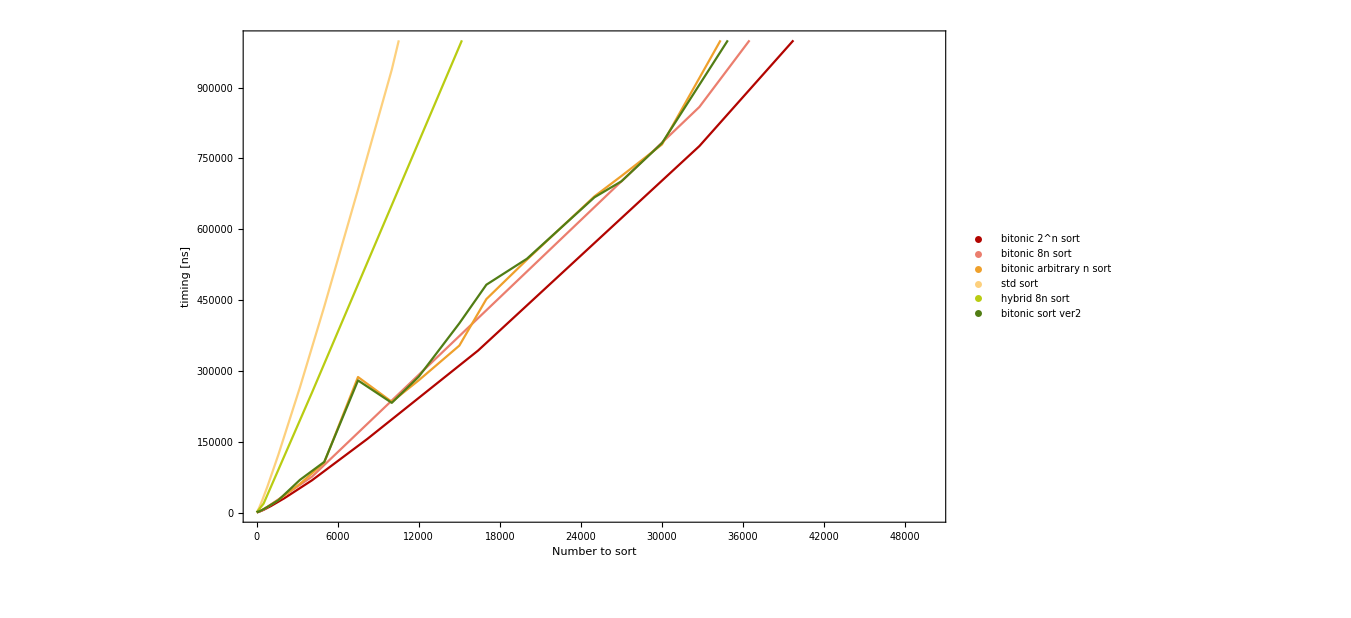

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4, p5, p6
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {4*10^4, 2.2*10^5}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0, 50000},{0, 10 ^6}},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

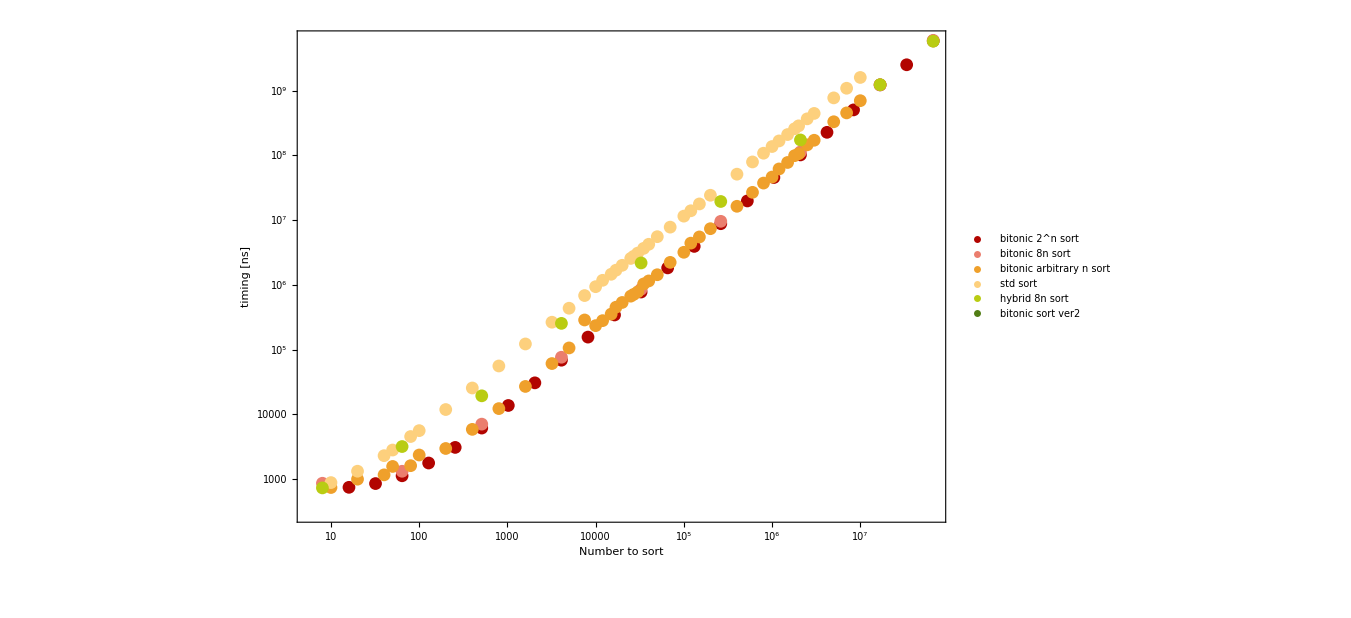

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLogLogPlot[{
p1,p2,p3,p4, p5
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]]},
Epilog->Inset[legenda, {1*10^6, 2*10^8}],
AxesOrigin->{-100, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->Automatic,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

```mathematica
NonlinearModelFit[Take[p1, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p2, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p3, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p4, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
```

FittedModel[37.1976 x+2.73928×10^-7 x^2+0.096705 x Log[x]^2]

FittedModel[-7.66962 x+3.54864×10^-8 x^2+0.289341 x Log[x]^2]

FittedModel[13.1607 x+3.98674×10^-7 x^2+0.201529 x Log[x]^2]

FittedModel[87.8324 x+9.3576×10^-8 x^2+0.270604 x Log[x]^2]

```mathematica
(*speedup calculation in comparison to std*)

speedup1=Table[{p3[[i,1]],p4[[i,2]]/p3[[i,2]]},{i,1,p3//Length}]//N;
```

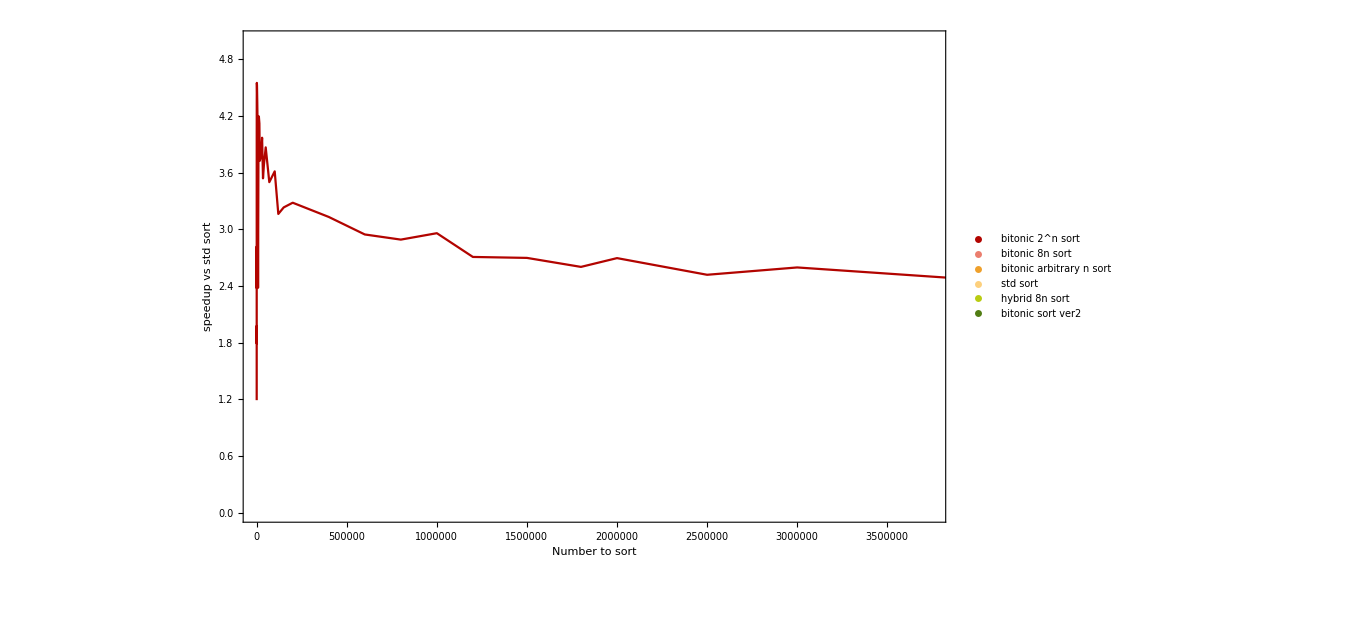

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{Automatic,{0,5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

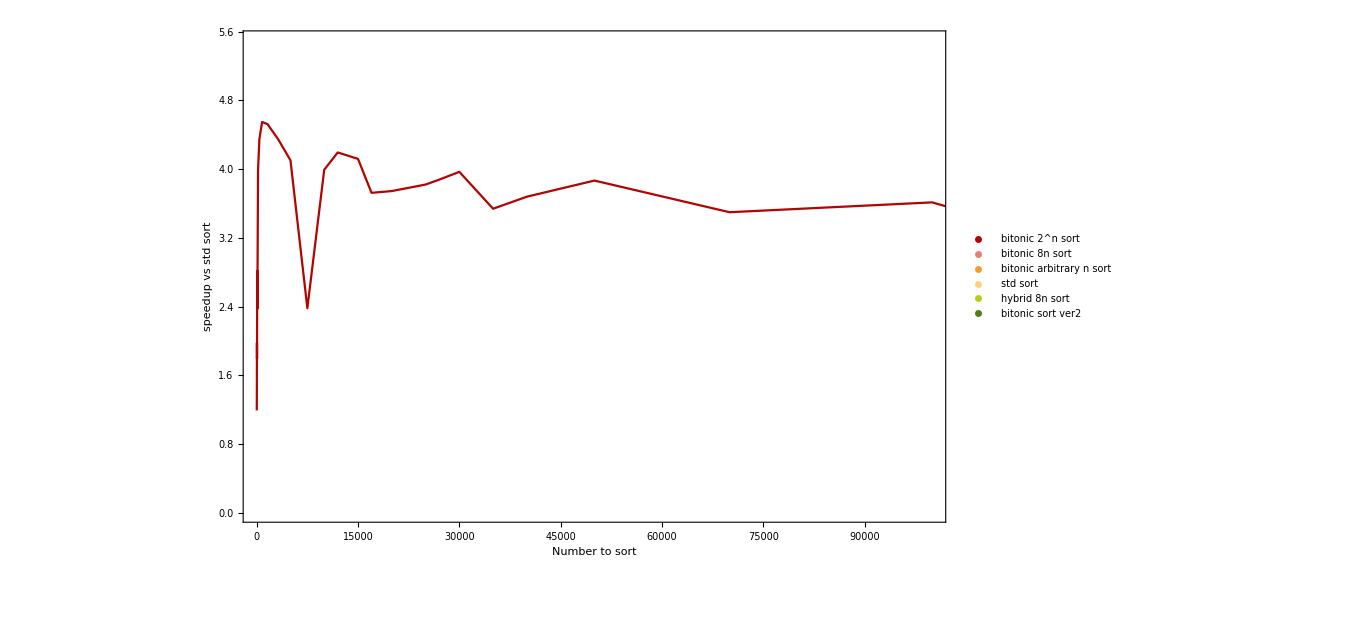

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0,100000},{0,5.5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```